```mathematica
SetDirectory@NotebookDirectory[];
(*Import["https://qtechtheory.org/QuESTlink.m"]
CreateDownloadedQuESTEnv[];*)
Import["QuESTlink.m"]
CreateLocalQuESTEnv["quest_link"];
```

## Bases

```mathematica
(*the threshold put in QuESTlink by hand*)
thresQuest=0.5;
```

```mathematica
(*Pauli matrices*)
PZ={{1.,0.},{0.,-1.}};
PX={{0.,1.},{1.,0.}};
PY={{0.,-ⅈ},{ⅈ,0.}};
iden=IdentityMatrix[2];
(*Pauli bases*)
bas1P={iden,PX,PY,PZ};
bas2P={};
Do[(
Do[(
AppendTo[bas2P,KroneckerProduct[bas1P[[t1]],bas1P[[t2]]]]
),{t2,1,4,1}]
),{t1,1,4,1}];
```

```mathematica
Clifford={iden,PX,PY,PZ,(iden+ⅈ PX)/Sqrt[2],(iden-ⅈ PX)/Sqrt[2],(iden+ⅈ PY)/Sqrt[2],(iden-ⅈ PY)/Sqrt[2],(iden+ⅈ PZ)/Sqrt[2],(iden-ⅈ PZ)/Sqrt[2],(PX+PY)/Sqrt[2],(PX-PY)/Sqrt[2],(PX+PZ)/Sqrt[2],(PX-PZ)/Sqrt[2],(PY+PZ)/Sqrt[2],(PY-PZ)/Sqrt[2],(ⅈ iden+PX+PY+PZ)/2,(ⅈ iden-PX-PY+PZ)/2,(ⅈ iden+PX-PY-PZ)/2,(ⅈ iden-PX+PY-PZ)/2,(-ⅈ iden+PX+PY+PZ)/2,(-ⅈ iden-PX-PY+PZ)/2,(-ⅈ iden+PX-PY-PZ)/2,(-ⅈ iden-PX+PY-PZ)/2};
```

```mathematica
(*Ideal 2-qubit gate in experiment*)
uPhase={{1,0,0,ⅈ},{0,1,ⅈ,0},{0,ⅈ,1,0},{ⅈ,0,0,1}}/Sqrt[2];
```

```mathematica
(*Check normalization of Kraus operators, should return identity*)
checkKraus[basK_]:=(
res=ConstantArray[0,{4,4}];
size=Dimensions[basK][[1]];
Do[(
res+=basK[[t]]†.basK[[t]];
),{t,1,size,1}];
Clear[size];
Return[res]
)
```

```mathematica
(*Check whether Kraus operators pass for QuESTlink*)
checkForQuest[basK_]:=(
mat=checkKraus[basK];
deviation=Flatten[mat-IdentityMatrix[4]];
mag=Abs[Re[deviation]]+Abs[Im[deviation]];
Return[{Total[mag],Total[mag]<thresQuest}]
)
```

## Import Choi matrices

### Function

```mathematica
ChoiToKraus2[mat_]:=(
{evals,evecs}=Eigensystem[mat];
DD=Dimensions[evals][[1]];
set={};
Do[(
m=evecs[[d]]*Sqrt[evals[[d]]];
kmat={};
Do[(
row={};
Do[(
vec1=ConstantArray[0.,{4}];
vec2=ConstantArray[0.,{4}];
vec1[[s]]=1.0;
vec2[[t]]=1.0;
AppendTo[row,Flatten[TensorProduct[vec1,vec2]].m];
),{s,1,4,1}];
AppendTo[kmat,row];
),{t,1,4,1}];
AppendTo[set,kmat];
),{d,1,DD,1}];
Return[set]
)
```

### Import

```mathematica
allChois=Import["AllChois.mat"];
```

```mathematica
choi01=allChois[[1]];
choi02=allChois[[2]];
choi03=allChois[[3]];
choi12=allChois[[4]];
choi13=allChois[[5]];
choi23=allChois[[6]];
kraus01=ChoiToKraus2[choi01];
kraus02=ChoiToKraus2[choi02];
kraus03=ChoiToKraus2[choi03];
kraus12=ChoiToKraus2[choi12];
kraus13=ChoiToKraus2[choi13];
kraus23=ChoiToKraus2[choi23];
```

```mathematica
listSetKraus={kraus01,kraus02,kraus03,kraus12,kraus13,kraus23};
```

```mathematica
setKraus0={uPhase};
```

```mathematica
(*Check for QuESTlink*)
checkForQuest[kraus01]
checkForQuest[kraus02]
checkForQuest[kraus03]
checkForQuest[kraus12]
checkForQuest[kraus13]
checkForQuest[kraus23]
```

{0.273612,True}

{0.238223,True}

{0.112336,True}

{0.365054,True}

{0.241097,True}

{0.352457,True}

## Parameters

```mathematica
numQb=4;
numGt=8;
SamSize=20000;
```

```mathematica
GateGraph={3,2,1,0,2,1,0,3,1,0,3,2,2,1,0,3};
```

## QuESTlink

### Circuits

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,gates_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=Min[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
q2=Max[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
AppendTo[circ,Subscript[U, q1,q2][uPhase]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Return[circ]
)
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,gates_,set_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=Min[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
q2=Max[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
indK=q2+Min[2*q1,3];
AppendTo[circ,Subscript[Kraus, q2,q1][set[[indK]]]];(*note the order of q1, q2 is the opposite of the order in direct calculation*)
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Return[circ]
)
```

```mathematica
gates0=Table[IdentityMatrix[2],numQb+2*numGt];
```

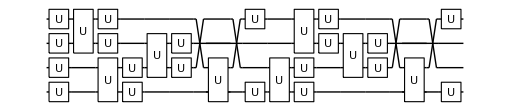

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,gates0];
DrawCircuit@circI
```

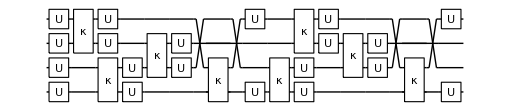

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,gates0,listSetKraus];
DrawCircuit@circN
```

### Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,SamSize_,set_]:=(
Err={};
Fid={};
Do[(
err1={};
AppendTo[Err,err1];
),{t,0,numQb-1,1}];
Do[(
gates=RandomVariate[CircularUnitaryMatrixDistribution[2],numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,set];
ApplyCircuit[circI,ψIN,ψOUT];
ApplyCircuit[circN,ρIN,ρOUT];
nn=CalcTotalProb[ρOUT];
Do[(
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, t],ψWP];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, t],ρWP];
AppendTo[Err[[t+1]],(ZN/nn-ZI)/2];
),{t,0,numQb-1,1}];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,SamSize_,set_]:=(
Err={};
Fid={};
Do[(
err1={};
AppendTo[Err,err1];
),{t,0,numQb-1,1}];
Do[(
gates=RandomChoice[Clifford,numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,set];
ApplyCircuit[circI,ψIN,ψOUT];
ApplyCircuit[circN,ρIN,ρOUT];
nn=CalcTotalProb[ρOUT];
Do[(
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, t],ψWP];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, t],ρWP];
AppendTo[Err[[t+1]],(ZN/nn-ZI)/2];
),{t,0,numQb-1,1}];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

### Simulation

```mathematica
US=SamplingU[numQb,numGt,GateGraph,SamSize,listSetKraus];
CS=SamplingC[numQb,numGt,GateGraph,SamSize,listSetKraus];
```

{0.00256205,0.0000261974}

{0.00249914,0.0000261974}

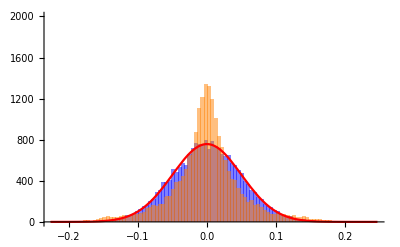

```mathematica
q=0;(*qubit label = 0, 1, 2, or 3*)
US1=US[[1]][[q+1]];
CS1=CS[[1]][[q+1]];
{Moment[US1,2],Sqrt[(Moment[US1,4]-Moment[US1,2]^2)/SamSize]}
{Moment[CS1,2],Sqrt[(Moment[US1,4]-Moment[US1,2]^2)/SamSize]}
xMax=Max[{Max[US1],Max[CS1]}];
xMin=Min[{Min[US1],Min[CS1]}];
dx=(xMax-xMin)/100;
HUplot=Histogram[US1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS1,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
σ=Sqrt[Moment[CS1,2]];
NDplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,NDplot,PlotRange->{{xMin,xMax},{0,SamSize/10}}]
```

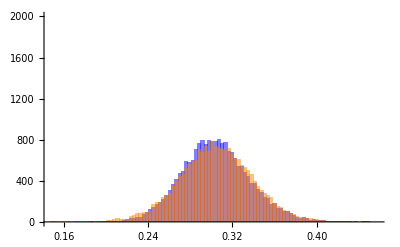

```mathematica
xMax=Max[{Max[US[[2]]],Max[CS[[2]]]}];
xMin=Min[{Min[US[[2]]],Min[CS[[2]]]}];
dx=(xMax-xMin)/100;
HUplot=Histogram[US[[2]],{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS[[2]],{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
Show[HUplot,HCplot,PlotRange->{{xMin,xMax},{0,SamSize/10}}]
```

```mathematica
CreateFile["CS-expChoi-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-q"<>ToString[q]<>".dat"];
file=File["CS-expChoi-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-q"<>ToString[q]<>".dat"];
Data={};
AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]][[q+1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,CS[[1]][[q+1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
Export[file,Data];
```

## Direct calculation

### Functions on 4 qubits

```mathematica
applyU1Gate[mat_,q_,ρ_]:=(
If[q==0, res=KroneckerProduct[mat,KroneckerProduct[iden,KroneckerProduct[iden,iden]]]];
If[q==1, res=KroneckerProduct[iden,KroneckerProduct[mat,KroneckerProduct[iden,iden]]]];
If[q==2, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[mat,iden]]]];
If[q==3, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[iden,mat]]]];
Return[res.ρ.ConjugateTranspose[res]]
)
```

```mathematica
singMeas0[q_,ρ_]:=(
mat=ConstantArray[0.,{2,2}];
mat[[1,1]]=1.0;
res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[iden,iden]]];
If[q==0, res=KroneckerProduct[mat,KroneckerProduct[iden,KroneckerProduct[iden,iden]]]];
If[q==1, res=KroneckerProduct[iden,KroneckerProduct[mat,KroneckerProduct[iden,iden]]]];
If[q==2, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[mat,iden]]]];
If[q==3, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[iden,mat]]]];
Return[Tr[res.ρ]]
)
```

```mathematica
singMeasZ[q_,ρ_]:=(
res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[iden,iden]]];
If[q==0, res=KroneckerProduct[PZ,KroneckerProduct[iden,KroneckerProduct[iden,iden]]]];
If[q==1, res=KroneckerProduct[iden,KroneckerProduct[PZ,KroneckerProduct[iden,iden]]]];
If[q==2, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[PZ,iden]]]];
If[q==3, res=KroneckerProduct[iden,KroneckerProduct[iden,KroneckerProduct[iden,PZ]]]];
Return[Tr[res.ρ]]
)
```

```mathematica
swap2=0.5*(IdentityMatrix[4]+KroneckerProduct[PX,PX]+KroneckerProduct[PY,PY]+KroneckerProduct[PZ,PZ]);
swap01=KroneckerProduct[swap2,KroneckerProduct[iden,iden]];
swap12=KroneckerProduct[iden,KroneckerProduct[swap2,iden]];

swap3=0.5*(IdentityMatrix[8]+KroneckerProduct[PX,KroneckerProduct[iden,PX]]+KroneckerProduct[PY,KroneckerProduct[iden,PY]]+KroneckerProduct[PZ,KroneckerProduct[iden,PZ]]);
swap02=KroneckerProduct[swap3,iden];
swap13=KroneckerProduct[iden,swap3];
```

```mathematica
applyKraus2[setK_,q1_,q2_,ρ_]:=(
numK=Dimensions[setK][[1]];
If[q1==0,(resI=ρ;
If[q2==2,resI=swap12.ρ.swap12];
If[q2==3,resI=swap13.ρ.swap13];)];
If[q1==1,(resI=swap01.ρ.swap01;
If[q2==2,resI=swap12.resI.swap12];
If[q2==3,resI=swap13.resI.swap13])];
If[q1==2,resI=swap13.swap02.ρ.swap02.swap13];
sum=ConstantArray[0.,{16,16}];
Do[(
mat=KroneckerProduct[setK[[t]],IdentityMatrix[4]];
sum+=mat.resI.ConjugateTranspose[mat];
),{t,1,numK,1}];
If[q1==0,(resII=sum;If[q2==2,resII=swap12.sum.swap12];If[q2==3,resII=swap13.sum.swap13];)];
If[q1==1,(If[q2==2,resII=swap12.sum.swap12];
If[q2==3,resII=swap13.sum.swap13];
resII=swap01.resII.swap01;)];
If[q1==2,resII=swap13.swap02.sum.swap02.swap13];
Return[resII]
)
```

```mathematica
noisyCirc[ρI_,numGt_,GateGraph_,gates_,set_]:=(
ρ=ρI;
Do[(
g=gates[[q+1]];
ρ=applyU1Gate[g,q,ρ];
),{q,0,numQb-1,1}];
Do[(
q1=Min[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
q2=Max[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
indK=q2+Min[2*q1,3];
ρ=applyKraus2[set[[indK]],q1,q2,ρ];
g=gates[[numQb+2*t+1]];
ρ=applyU1Gate[g,q1,ρ];
g=gates[[numQb+2*t+2]];
ρ=applyU1Gate[g,q2,ρ];
),{t,0,numGt-1,1}];
Return[ρ]
)
```

```mathematica
idealCirc[ρI_,numGt_,GateGraph_,gates_]:=(
ρ=ρI;
Do[(
g=gates[[q+1]];
ρ=applyU1Gate[g,q,ρ];
),{q,0,numQb-1,1}];
Do[(
q1=Min[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
q2=Max[GateGraph[[2*t+1]],GateGraph[[2*t+2]]];
indK=q2+Min[2*q1,3];
ρ=applyKraus2[setKraus0,q1,q2,ρ];
g=gates[[numQb+2*t+1]];
ρ=applyU1Gate[g,q1,ρ];
g=gates[[numQb+2*t+2]];
ρ=applyU1Gate[g,q2,ρ];
),{t,0,numGt-1,1}];
Return[ρ]
)
```

```mathematica
SampU[numQb_,numGt_,GateGraph_,SamSize_,set_]:=(
Err={};
Fid={};
Do[(
err1={};
AppendTo[Err,err1];
),{qq,0,numQb-1,1}];
Do[(
gates=RandomVariate[CircularUnitaryMatrixDistribution[2],numQb+2*numGt];
ρinit=ConstantArray[0.,{16,16}];
ρinit[[1,1]]=1.0;
ρN=noisyCirc[ρinit,numGt,GateGraph,gates,set];
ρI=idealCirc[ρinit,numGt,GateGraph,gates];
AppendTo[Fid,1-Tr[ρN.ρI]];
(*nn=Tr[ρN];*)
Do[(
pI=singMeas0[qq,ρI];
pN=singMeas0[qq,ρN];
(*AppendTo[Err[[qq+1]],(pN/nn)-pI];*)
AppendTo[Err[[qq+1]],pN-pI];
),{qq,0,numQb-1,1}]
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SampC[numQb_,numGt_,GateGraph_,SamSize_,set_]:=(
Err={};
Fid={};
Do[(
err1={};
AppendTo[Err,err1];
),{qq,0,numQb-1,1}];
Do[(
gates=RandomChoice[Clifford,numQb+2*numGt];
ρinit=ConstantArray[0.,{16,16}];
ρinit[[1,1]]=1.0;
ρN=noisyCirc[ρinit,numGt,GateGraph,gates,set];
ρI=idealCirc[ρinit,numGt,GateGraph,gates];
AppendTo[Fid,1-Tr[ρN.ρI]];
(*nn=Tr[ρN];*)
Do[(
pI=singMeas0[qq,ρI];
pN=singMeas0[qq,ρN];
(*AppendTo[Err[[qq+1]],(pN/nn)-pI];*)
AppendTo[Err[[qq+1]],pN-pI];
),{qq,0,numQb-1,1}]
),SamSize];
Return[{Err,Fid}]
)
```

### Simulation

```mathematica
{USall,fidU}=SampU[numQb,numGt,GateGraph,SamSize,listSetKraus];
{CSall,fidC}=SampC[numQb,numGt,GateGraph,SamSize,listSetKraus];
```

{0.0027443,0.0000282623}

{0.00278759,0.0000282623}

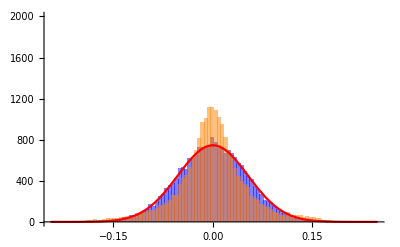

```mathematica
q=0;
US=Re[USall[[q+1]]];
CS=Re[CSall[[q+1]]];
{Moment[US,2],Sqrt[(Moment[US,4]-Moment[US,2]^2)/SamSize]}
{Moment[CS,2],Sqrt[(Moment[US,4]-Moment[US,2]^2)/SamSize]}
xMax=Max[{Max[US],Max[CS]}];
xMin=Min[{Min[US],Min[CS]}];
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
σ=Sqrt[Moment[CS,2]];
NDplot=Plot[SamSize*dx*PDF[NormalDistribution[0,σ],x]//Evaluate,{x,xMin,xMax},PlotStyle->{Red},PlotRange->All];
Show[HUplot,HCplot,NDplot,PlotRange->{{xMin,xMax},{0,SamSize/10}}]
```

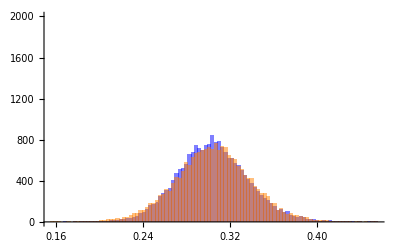

```mathematica
US=Re[fidU];
CS=Re[fidC];
xMax=Max[{Max[US],Max[CS]}];
xMin=Min[{Min[US],Min[CS]}];
dx=(xMax-xMin)/100;
HUplot=Histogram[US,{xMin,xMax,dx},ChartStyle->Opacity[.5,Blue]];
HCplot=Histogram[CS,{xMin,xMax,dx},ChartStyle->Opacity[.5,Orange]];
Show[HUplot,HCplot,PlotRange->{{xMin,xMax},{0,SamSize/10}}]
```

```mathematica
CreateFile["CS-expChoi-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-q"<>ToString[q]<>".dat"];
file=File["CS-expChoi-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-q"<>ToString[q]<>".dat"];
Data={};
AppendTo[Data,"US-Err:"];AppendTo[Data,Re[USall[[q+1]]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,Re[fidU]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,Re[CSall[[q+1]]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,Re[fidC]];AppendTo[Data,""];
Export[file,Data];
```